## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["AnalyticalSolarDevices`","C:\\Users\\Liu Haohui\\OneDrive - envision\\Development\\Analytical models development\\analytical-solar-cell-and-module\\AnalyticalSolarDevices.wl"];
T=298.15;
spec=<<spectrum_AM15G;
```

## Calculate cell output under a particular spectrum and temperature

Single junction cells

```mathematica
SiCell[spec,T]
```

{{{0.746883,-7.82107×10^-11},{0.746883,-7.73585×10^-11},{0.721987,209.826},{0.709539,277.729},{0.697091,325.937},{0.672195,381.023},{0.662859,392.426},{0.653523,400.68},{0.648855,403.901},{0.644187,406.635},{0.639519,408.955},{0.634851,410.925},{0.616179,416.253},{0.597507,419.055},{0.44813,422.59},{0.298753,422.82},{0.149377,422.973},{0.,423.123},{-0.149377,423.272},{-0.298753,423.421},{-0.44813,423.571},{-0.597507,423.72},{-0.746883,423.87},{-0.89626,424.019}},423.136,0.746883,0.829257,262.073,403.901,0.648855}

```mathematica
SiCell[spec,T,{"V",0.3}]
```

{126.845,422.818,0.3}

```mathematica
SiCell[spec,T,CellParameters->parameters["PERC"],CellQE->EQE["PERC"]]
```

{{{0.669707,-1.66294×10^-10},{0.647383,132.92},{0.62506,238.269},{0.602736,312.444},{0.585993,348.607},{0.569251,371.44},{0.560879,379.1},{0.556694,382.202},{0.552508,384.891},{0.548322,387.217},{0.544137,389.223},{0.535765,392.436},{0.50228,398.738},{0.468795,400.526},{0.401824,401.206},{0.267883,401.389},{0.133941,401.523},{0.,401.657},{-0.133941,401.791},{-0.267883,401.925},{-0.401824,402.059},{-0.535765,402.193},{-0.669707,402.327},{-0.803648,402.461},{-0.937589,402.594}},401.693,0.669707,0.790916,212.769,382.202,0.556694}

```mathematica
GaAsCell[spec,T]
```

{{{1.11024,3.71977×10^-13},{1.07323,159.568},{1.05472,211.506},{1.03622,246.17},{1.02697,258.173},{0.999212,279.56},{0.992273,282.576},{0.985334,284.987},{0.978395,286.913},{0.971456,288.452},{0.957578,290.669},{0.9437,292.1},{0.888188,294.377},{0.666141,295.297},{0.444094,295.526},{0.222047,295.748},{0.,295.97},{-0.222047,296.192},{-0.444094,296.414},{-0.666141,296.637},{-0.888188,296.859}},296.,1.11024,0.854481,280.808,284.987,0.985334}

InGaP/Si tandem cell IV curve

```mathematica
output=TwoTer$InGaPSi[spec,T,CouplingEfficiency->0.5]
```

{{{-0.0362837,146.673},{0.110453,146.527},{0.257044,146.38},{0.403488,146.234},{0.549785,146.088},{0.694475,145.942},{1.91938,144.118},{1.98746,142.294},{2.0147,140.469},{2.03168,138.645},{2.0536,134.996},{2.06823,131.348},{2.08813,124.051},{2.10204,116.754},{2.12175,102.159},{2.13603,87.5653},{2.15684,58.3768},{2.17226,29.1884},{2.18466,0.}},146.673,2.18466,0.883195,283.004,140.469,2.0147,145.942,217.511}

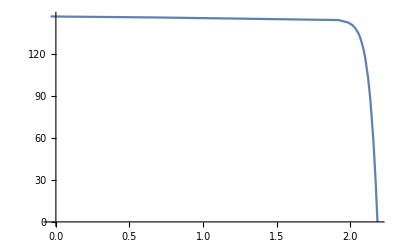

```mathematica
ListLinePlot[output[[1]],PlotRange->Full]
```

GaAs cell with various shunts.

```mathematica
Rsh={100,500,1000,5000,10000}*10^-4;
```

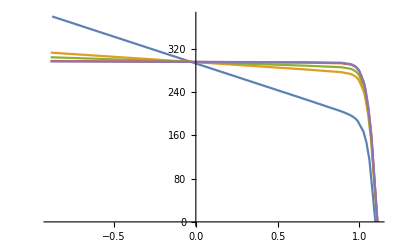

```mathematica
outputs=GaAsCell[spec,T,CellParameters-><|"J01"->6*^-17,"J02"->1*^-8,"Rs"->1*^-4,"Rsh"->#|>]&/@Rsh;
ListLinePlot[outputs[[All,1]],PlotRange->Full]
```

## Investigate the effect of temperature

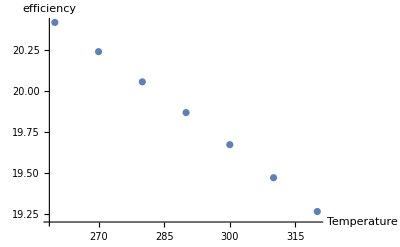

```mathematica
Temp=Range[260,320,10];
eff=Table[InGaPCell[spec,t][[5]]/10,{t,Temp}];
ListPlot[{Temp,eff}//Transpose,AxesLabel->{"Temperature","efficiency"}]
```

## Investigate effect of coupling efficiency

{29.1142,29.1252,29.1359,29.1463,29.1566,29.1667,29.1766,29.1864}

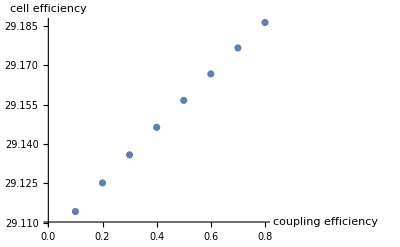

```mathematica
couplingEff=Range[0.1,0.8,0.1];
eff=Table[TwoTer$GaAsSi[spec,T,CouplingEfficiency->eta][[5]]/10,{eta,couplingEff}]
ListPlot[{couplingEff,eff}//Transpose,AxesLabel->{"coupling efficiency","cell efficiency"}]
```